# Regression Model Project -

## Predicting Boston House Prices With Regression

## Introduction -Graphics-

We will develop and evaluate the performance and prediction potential of a model trained and tested using data collected from residences in Boston’s suburbs as part of this study. We will do this by exploring various different machine learning algorithms.
We’ll use this model to forecast the monetary class worth of a house in the Boston region after we’ve found a satisfactory fit.
A real estate agent who could use the information offered on a daily basis would benefit greatly from a model like this.

### About the dataset

The dataset used in this project comes from the UCI Machine Learning Repository. Each of the 506 items in this database was gathered in 1970 from the Boston Standard Metropolitan Statistical Area (SMSA) and includes aggregate information about 14 attributes of residences in various Boston areas.

The features can be summarized as follows :

Sl. No | Features | Description
1 | CRIM | per capita crime rate by town
2 | ZN | proportion of residential land zoned for lots over 25,000 sq.ft.
3 | INDUS | proportion of non-retail business acres per town.
4 | CHAS | Charles River dummy variable (1 if tract bounds river;0 otherwise)
5 | NOX | nitric oxides concentration (parts per 10 million)
6 | RM | average number of rooms per dwelling
7 | AGE | proportion of owner-occupied units built prior to 1940
8 | DIS | weighted distances to five Boston employment centres
9 | RAD | index of accessibility to radial highways
10 | TAX | full-value property-tax rate per $10,000
11 | PTRATIO | pupil-teacher ratio by town
12 | B | 1000(Bk-0.63)^2 where Bk is the proportion of blacks by town
13 | LSTAT | % lower status of the population
14 | MEDV | Median value of owner-occupied homes in $1000's

#### Import Dataset :

Import[] - 		Imports data from source, returning a Wolfram Language representation of it.
Dataset[] - 		Represents a structured dataset based on a hierarchy of lists and associations.
Flatten[] - 		used to flatten out nested lists.
Map[] - 		          applies a particular function to each and ever element/list
Association[] - 	represents an association between keys and values. We use i here to represent the header in the dataset.
StringSplit[] - 		splits “string” into a list of substrings separated by whitespace.
ToExpression[] -      gives the expression obtained by interpreting strings as Wolfram Language input(Reals).

We import that dataset for further use in the project . Since the data is in the form of CSV separated by “Whitespace” , we use ‘StringSplit[]’, followed by ToExpression to convert string into Reals. We also set seed, to keep he random generation predictable.

```mathematica
SeedRandom[21200301];
```

```mathematica
(*Import CSV file*)
data=Import[NotebookDirectory[]<>"housing.csv", "CSV","Numeric"->True];
```

```mathematica
(*Extract numerical values seperated by space*)
data//MatrixForm;
For[i=1,i<= Length[data] ,i++,data[[i]] = Flatten[StringSplit[data[[i]],WhitespaceCharacter..]]]
```

```mathematica
(*Convert String values to Reals*)
data = Dataset[ToExpression[data]];
(*Add header/column names*)
header = {"CRIM","ZN","INDUS","CHAS","NOX","RM","AGE","DIS","RAD","TAX","PTRATIO","B","LSTAT","MEDV"}
data=Thread[header->#]&/@data//Map[Association]//Dataset;

(*Overview of dataset*)
Dataset[data, MaxItems->6]
```

{CRIM,ZN,INDUS,CHAS,NOX,RM,AGE,DIS,RAD,TAX,PTRATIO,B,LSTAT,MEDV}

```mathematica
Dimensions[data]
```

{506,14}

The above Boston Housing dataset contains 506 observations and 14 variables including the target variable ‘MEDV’

## Exploratory Data Analysis

In this section, we explore the data by looking at it’s features and determine a few significant variables for conducting Multiple Linear Regression.

For the purpose of the project the dataset has been preprocessed as follows :

The essential features for the project are will be determined and kept. The remaining features have been excluded.

16 data points with a ‘MEDV’ value of 50.0 have been removed. As they likely contain censored or missing values.

1 data point with a ‘RM’ value of 8.78 it is considered an outlier and has been removed for the optimal performance of the model.

As this data is out of date, the ‘MEDV’ value has been scaled multiplicatively to account for 35 years of market inflation.

CHAS has no or 0 correlation with the target, hence proving to be of no importance. We discard this data column.

### Data Processing

Few terms to remember

Histogram - A histogram is a graphical representation that organizes a group of data points into user-specified ranges. Similar in appearance to a bar graph, the histogram condenses a data series into an easily interpreted visual by taking many data points and grouping them into logical ranges or bins.

Boxplot - Boxplot is a method for graphically demonstrating the locality, spread and skewness groups of numerical data through their quartiles. There can be lines (called whiskers) extending from the box on a box plot, suggesting variability beyond the upper and lower quartiles; consequently, the plot is also known as the box-and-whisker plot or the box-and-whisker diagram. Individual points beyond the whiskers on the box-plot can be represented as outliers that deviate considerably from the rest of the dataset.

Correlation - A mutual relationship or connection between two or more things.
A new correlation function is created to ease the use of Dataset columns. Dataset cannot be passed directly onto the ‘Correlation[]’ function. Each column needs to be ‘normalized’ before its use. 
Correlation acts as a main factor to be determined for feature selection. If the correlation between any feature and target variable is less, it does not add a significance to the Regression.

```mathematica
corr[x_, y_]:= Correlation[Normal[data[All,x]],Normal[data[All,y]]];
```

We will first check for any missing data

```mathematica
Count[data,_Missing]
```

0

#### Price of homes : MEDV

Price is the target variable in the dataset. We now view the distribution of data of Boston House prices.

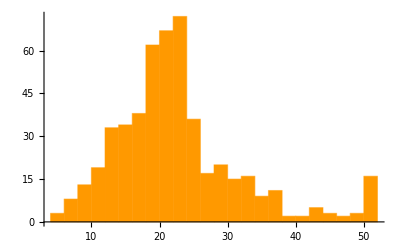

```mathematica
Histogram[Normal[data[All,"MEDV"]],15, ChartStyle->Hue[.1]]
```

We can observe that there are a few house prices that act as an outlier, which may tend for it to interfere with the statistics of house prices.

#### RM - number of rooms per dwelling

We will now examine for outlier for ‘RM’ column which is the average number of rooms per dwelling. It is understood that the number of rooms in the house directly affects the cost of the house(Mostly irrespective of it’s size)

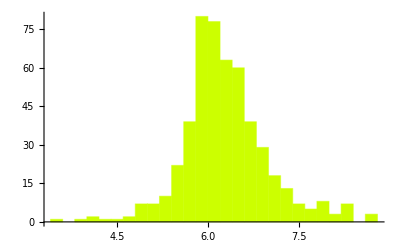

```mathematica
Histogram[data[All,"RM"], ChartStyle->Hue[.2]]
```

```mathematica
corr["MEDV","RM"]
```

0.69536

#### CRIME - Crime Ratio

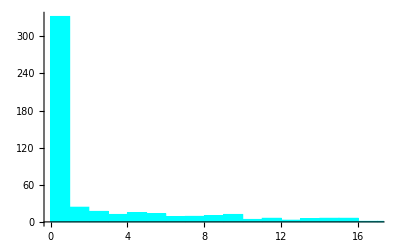

```mathematica
Histogram[data[All,"CRIM"],70, ChartStyle->Hue[.5]]
```

As we can observe, the crime rate of most areas seem to be low, even with the increase in the number of breaks, the graph ratio seems to not decrease. We can view the correlation between price and crime ratio to find if it is important.

```mathematica
corr["MEDV","CRIM"]
```

-0.388305

#### CHAS - Whether or not if the house is bounded by the tract of river Charles

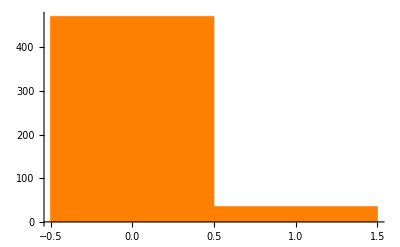

```mathematica
Histogram[data[All,"CHAS"], ChartStyle->Orange]
```

CHAS is a binary variable which takes values 0 and 1. ‘1’ indicates that the house is in the banks or surrounded by river Charles. There seem to be 100 times more houses in the city than in the tracts of the river.

```mathematica
corr["MEDV","CHAS"]
```

0.17526

Since the variable hold not much information in relationship to our target variable, we drop this variable as a part of  the project

#### AGE - age of the houses

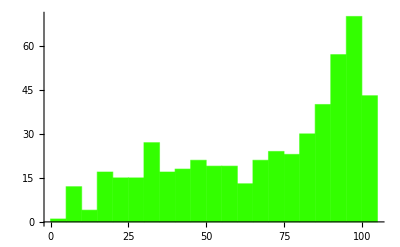

```mathematica
Histogram[data[All,"AGE"],20, ChartStyle->Hue[.3]]
```

```mathematica
corr["MEDV","AGE"]
```

-0.376955

#### RAD - accessibility to radial highways

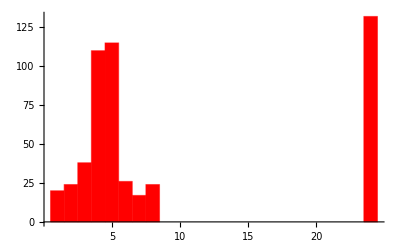

```mathematica
Histogram[data[All,"RAD"],30, ChartStyle->Red]
```

The above seems to describe that there are only a few areas closer to the highways and others are mostly far.

```mathematica
corr["MEDV","RAD"]
```

-0.381626

#### PTRATIO - this is the pupil teacher ratio in the area

```mathematica
corr["MEDV","PTRATIO"]
```

-0.507787

#### B - proportion of blacks by town

```mathematica
corr["MEDV","B"]
```

0.333461

#### LSTAT - % lower status of the population

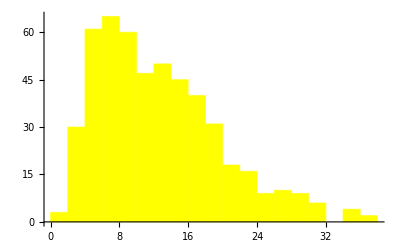

```mathematica
Histogram[data[All,"LSTAT"],ChartStyle->Yellow]
```

```mathematica
corr["MEDV","LSTAT"]
```

-0.737663

The data is normally distributed and LSTAT feature has a very high negative correlation with price variable.

#### TAX

```mathematica
corr["MEDV","TAX"]
```

-0.468536

#### NOX - Nitric Oxide levels in air in parts per million

```mathematica
corr["MEDV","NOX"]
```

-0.427321

#### Data out of date :

Since the data was recorded in the year 1970, there prices do not match 2022. Hence,  we look at the inflation graph for more information on the inflation rate.
-Graphics-
After closely looking at the graph, we scale the “MEDV” parameter by 2.5 (approximately 250% inflation)

```mathematica
data= Normal[data];
data[[All,"MEDV"]]=Flatten[data[[All,"MEDV"]]]*2.5;
data = Dataset[data];
```

Let us now visualize the statistics again :

```mathematica
Framed[TableView[{{"Maximum",Max[data[All,"MEDV"]]},{"Minimum" ,Min[data[All,"MEDV"]]},{"Mean",Mean[data[All,"MEDV"]]},{"Median",Median[data[All,"MEDV"]]},{"Standard Deviation",StandardDeviation[data[All,"MEDV"]]}},AllowedDimensions->{2,5},AppearanceElements->{},Background->LightYellow],FrameStyle->{Black,Thickness[3]}, FrameMargins->None]
```

Maximum125.Minimum12.5Mean56.33201581027668Median53.Standard Deviation22.99276021844954

The highest price for a Boston House is $ 122,000 and the lowest is at $ 12,500.

### Feature Selection

Data science is the process of creating assumptions and hypotheses based on data and putting them to the test through various activities. Features have been selected based on their correlation with the target variable. Only features with correlation >  ±50 is chosen. For each feature, we could make the following intuitive assumptions at first :

Houses with more rooms (and hence a higher ‘RM’ value) will be more valuable. Houses with more rooms are usually larger and can accommodate more people, therefore it’s understandable that they cost more. They are variables with a direct proportional relationship.

Neighborhoods having a larger proportion of lower-class employees (higher ‘LSTAT’ score) will be less valuable. If the number of lower-income people is larger, it is more probable that they have limited purchasing power and, as a result, their homes will be less expensive. They are variables that are inversely proportional.

The value of neighbourhoods having a greater student-to-teacher ratio (a higher ‘PTRATIO’ number) will be lower. If the student-to-teacher ratio is greater, it is likely that there are fewer schools in the community. This might be due to lower tax revenue, which could be because individuals in that neighbourhood make less money. People’s homes are likely to be worth less if they earn less money. They are variables that are inversely proportional.

The NOX - nitric oxide concentration in air in parts per million. The legal airborne permissible exposure limit (PEL) is 5 ppm, not to be exceeded at any time. This acts as one of main reasons for depletion of Ozone layer. Nitric Oxide combining with water vapour forms Nitric Acid, making the environment acidic enough to destroy the ozone layer hence letting in harmful rays. This directly affects the occupation of a particular area. It seems to carry an inverse relationship with price.

TAX - charged in a particular area, decides the level of occupation and rates of houses in the area. As TAX in that particular area increases, the value of the property decreases, since occupancy is limited due to high rates.

The 5 features chosen are, ‘RM’, ‘LSTAT’, ‘PTRATIO’, NOX’ and ‘TAX’.

#### Outliers Reduction

We can note that there are many outliers. Outliers are data points that are far from other data points. In other words, they’re unusual values in a dataset. Outliers are problematic for many statistical analyses because they can cause tests to either miss significant findings or distort real results. Outliers are to be removed for optimum performance of the model.

The goal is to eliminate room values which exceeds normal limits . This increases the model’s robustness and likelihood of generalisation to new(test) data, which is the core purpose of machine learning.

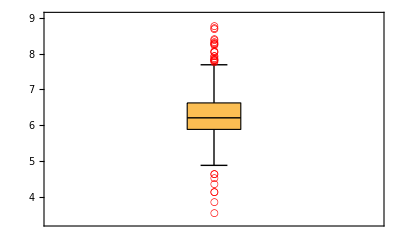

```mathematica
BoxWhiskerChart[data[All,"RM"],{{"Whiskers",Thick},{"Outliers",Style["○",Red]},{"MedianMarker",Directive[Thick,Black]},{"Fences",Thick}},ChartStyle->{EdgeForm[{Black}]}]
```

```mathematica
RMoutlier = Select[data,#RM>8.6&];
RMoutlier[All,"RM"]
```

There are 3 outliers present with value of RM  = 8.78,8.704 and 8.725

```mathematica
data =Select[data,#RM<=8.6&];
```

The max value of MEDV seems odd from the statistics. From the original data description, it says: Variable #14 seems to be censored at 50.00 (corresponding to a median price of $50,000). Based on that, values above 50.00 may not help to predict MEDV. Let’s plot the dataset and see interesting trends/stats. We will find the outliers and remove those observations from the dataset which have value of price >= 50

```mathematica
data = Select[data,#MEDV<50*2.5&];
```

#### Data Statistics :

```mathematica
features= data[[All,{"RM","LSTAT","PTRATIO","NOX","TAX","MEDV"}]];

(*Numerical Statistics of chosen important variable*)

StringForm["Maximum : ``",Merge[features,Max]]
```

Maximum : …

```mathematica
StringForm["Minimum : ``",Merge[features,Min]]
```

Minimum : …

```mathematica
StringForm["Mean : ``",Dataset[Mean[features]]]
```

Mean : …

```mathematica
StringForm["Median : ``",Dataset[Median[features]]]
```

Median : …

```mathematica
StringForm["Standard Deviation : ``",Dataset[StandardDeviation[features]]]
```

Standard Deviation : …

We can see from the above statistics that the mean and median for ‘TAX’ variable is varying, this implies a skewed distribution. We will verify it’s significance in the later stages

```mathematica
Dimensions[features]
```

{489,6}

After outlier reduction, we are left with 6 variables and 489 observations.

#### Pairs Plot

Pair plot is used to understand the best set of features to explain a relationship between two variables or to form the most separated clusters. It also helps to form some simple classification models by drawing some simple lines or make linear separation in our data-set.

We are new to working with Datasets. Hence, the columns need to be normalized before it’s use. Hence, we create a function to make this easier and will use this in the future.

```mathematica
normalize[x_]:=Normal[features[All,x]];
```

```mathematica
Needs["StatisticalPlots`"]
```

Mathematica is a highly developed language which can import packages from sources like GitHub. Below, I have made use of it and imported ‘MathematicaForPredictionUtilities’ package to plot a pairs-plot easily by utilizing the function ‘VariableDependenceGrid[dataset]’

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MathematicaForPredictionUtilities.m"]
```

Importing from GitHub:  MosaicPlot.m

Importing from GitHub:  CrossTabulate.m

Importing from GitHub:  ParetoPrincipleAdherence.m

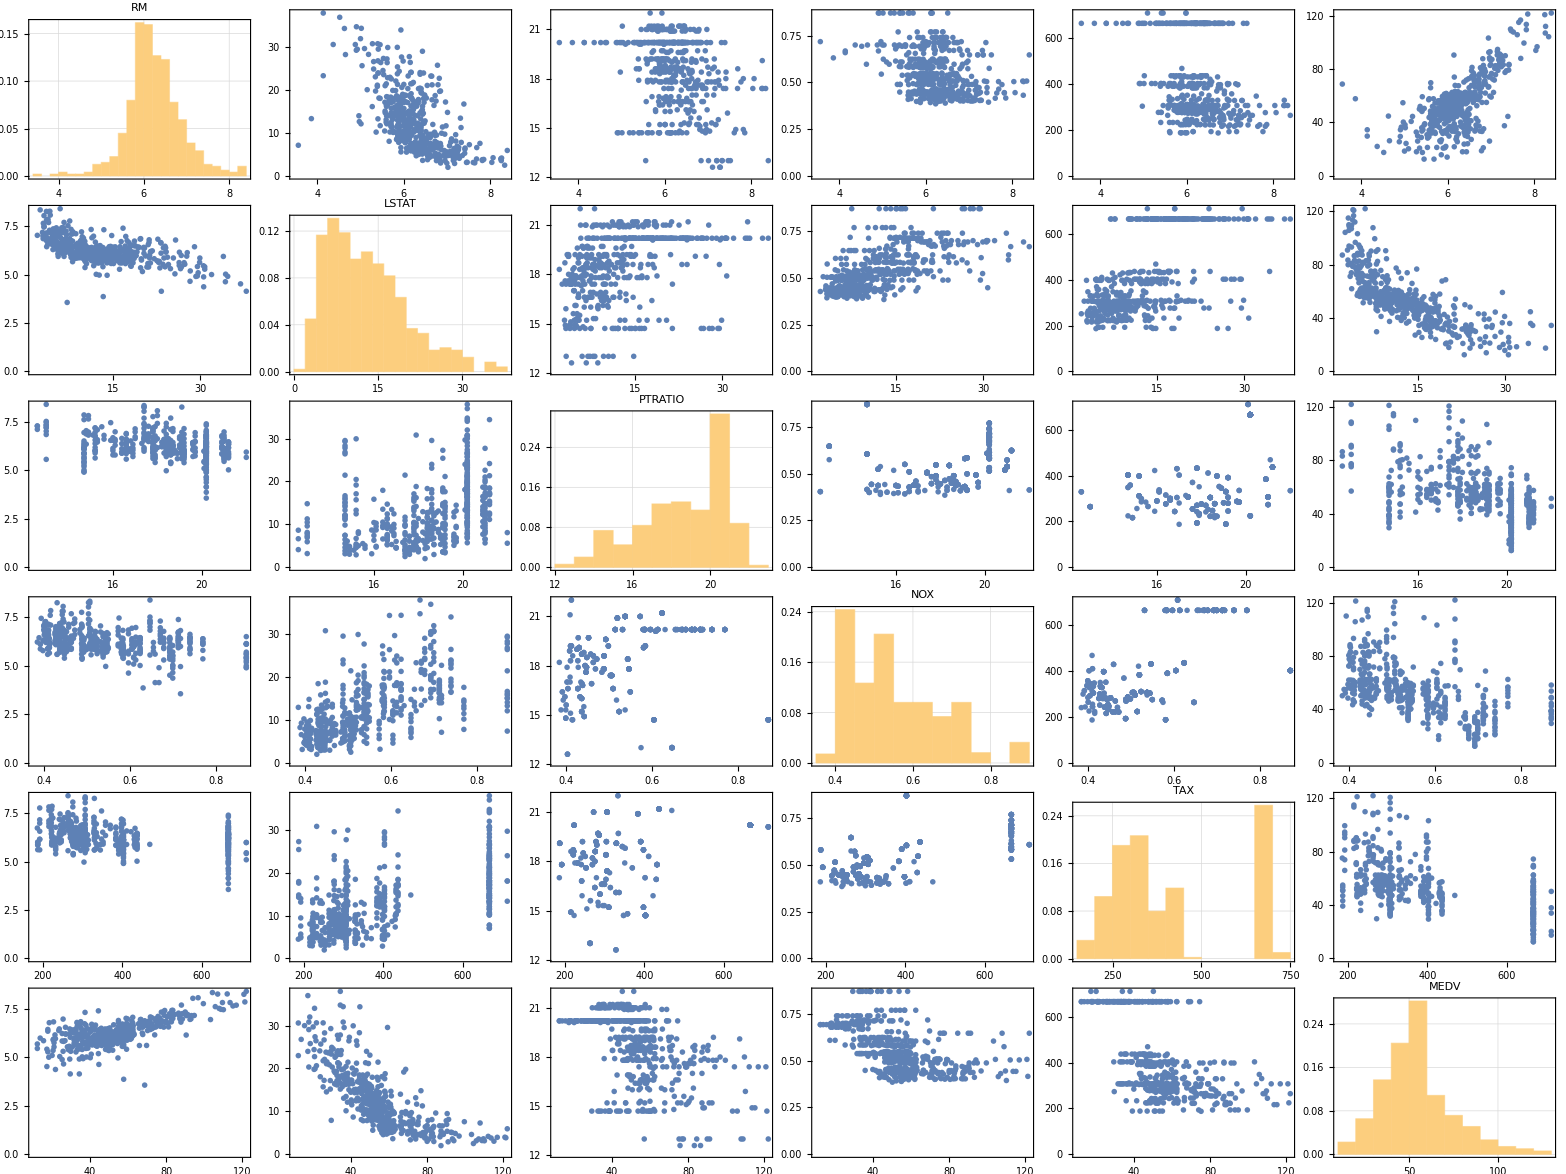

```mathematica
VariableDependenceGrid[features]
```

Mostly all the variables have somehow linear relationship between prices of Boston Houses.

## Machine Learning Models :

In this Section, we will be looking at different Machine Learning models to work with. The following are listed below

Support Vector Regression

Logistic Regression

Random Forest

Artificial Neural Network

Nearest Neighbours

#### Classify Target Variable

In order to run Machine Learning Classifier algorithm on a dataset, the data needs to be assigned to classes.
We will divide the price range for houses into 3 classes, low, medium and high.
We decide the values for splitting by getting 3 equal splits between minimum and maximum house price.

```mathematica
priceRange= (Max[features[All,"MEDV"]]-Min[features[All,"MEDV"]])/3
```

36.5

```mathematica
low = Min[features[All,"MEDV"]]+priceRange
med = Min[features[All,"MEDV"]]+2*priceRange
```

49.

85.5

Now we make use of the boundaries to classify the price of houses into a range/class using ‘Map’ function. We then append the list as an addition column to the existing dataset. 
For this we use ‘MapThread’ and ‘Append’

```mathematica
classify[p_]:=Which[p<=low, "low", low<p<=med, "med", p>med, "high"]
```

```mathematica
class=Map[classify, normalize["MEDV"]];
```

```mathematica
features=Dataset[MapThread[Append,{Normal[features],Thread["Class"->  class]}]];
```

We can now observe the classes the price is split into by using ‘Table’ and ‘Count’

```mathematica
Table[Count[normalize["Class"],i],{i,{"low","med","high"}}]
```

{201,251,37}

Number of houses with Low and Medium prices are almost equal when compared to the number of houses with High prices.

We will drop the “MEDV” from the dataset using ‘KeyDrop’ function.

```mathematica
features= KeyDrop[features,"MEDV"];
```

Now, let us split the data into train and test data. This is done using “TrainTestSplit”. It splits data into a pair of shuffled training and testing sets. The default splitting ratio is 80/20. We also use ‘SeedRandom’ to keep the train and test splits same every time.

```mathematica
{train,test}=ResourceFunction["TrainTestSplit"][#&/@features];

StringForm["Train : ``",Dimensions[train]]
StringForm["Test : ``",Dimensions[test]]
```

Train : {391,6}

Test : {98,6}

#### Dataset Modification

We will be using different Classifiers to classify the houses into different price ranges. Inorder to perform this, the classifiers require a data in specific format.  The data needs to be ‘labelled’, i.e., every observation in the dataset needs to be associated with its class.

```mathematica
train[1,All]//Normal
```

<|RM→6.657,LSTAT→21.22,PTRATIO→20.2,NOX→0.597,TAX→666.,Class→low|>

We can observe that the records are associated with it’s labels, but the observation is not associated to anything.

```mathematica
trainFinal=Flatten[Normal@train[1;;Length[train],{Most@#->Last@#}&],1];
testFinal=Flatten[Normal@test[1;;Length[test],{Most@#->Last@#}&],1];
trainFinal[[1]]
testFinal[[1]]
```

<|RM→6.657,LSTAT→21.22,PTRATIO→20.2,NOX→0.597,TAX→666.|>→low

<|RM→5.605,LSTAT→18.46,PTRATIO→19.1,NOX→0.431,TAX→330.|>→low

### Support Vector Machine :

#### Training

The objective of the support vector machine algorithm is to find a hyperplane in an N-dimensional space(N — the number of features) that distinctly classifies the data points.

Many people prefer the support vector machine because it delivers great accuracy while using less computing resources. SVM (Support Vector Machine) is a type of machine that may be used for both regression and classification. However, it is extensively employed in categorization goals.

-Graphics-

1 : Train the model with train dataset.

```mathematica
SVM = Classify[trainFinal,Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
Information[SVM,"MethodDescription"]
```

The support vector machine classifier separates the training data into two classes using a 
			maximum-margin hyperplane. The original feature space can be mapped into a higher dimensional space to 
			improve linear separability. The multi-class classification problem is reduced to a set of binary 
			classification problems.

2 : About the classifier

```mathematica
Information[SVM]
```

Classifier information
Data type | Mixed (number: 5)
Classes | ,,highlowmed
Accuracy | (80.6.) %
Method | SupportVectorMachine
Single evaluation time | 6.8 ms/example
Batch evaluation speed | 13.4 examples/ms
Loss | 0.532 ± 0.16
Model memory | 296. kB
Training examples used | 391 examples
Training time | 2.48 s
 |

#### Testing

We test the data by applying the classifier generated from the training set to the test set

```mathematica
testSVM = ClassifierMeasurements[SVM,testFinal];testSVM[{"Accuracy","RejectionRate","AreaUnderROCCurve"}]
```

{0.77551,0.,<|high→0.95,low→0.900986,med→0.851852|>}

We can view more features available

```mathematica
testSVM["Properties"]
```

{Accuracy,AccuracyBaseline,AccuracyRejectionPlot,AreaUnderROCCurve,BatchEvaluationTime,BestClassifiedExamples,CalibrationCurve,CalibrationData,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionDistribution,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,EvaluationTime,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeNumber,FalseNegativeRate,FalsePositiveExamples,FalsePositiveNumber,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LinearCalibrationCurve,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictiveValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,Report,ROCCurve,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TrueNegativeNumber,TruePositiveExamples,TruePositiveNumber,WorstClassifiedExamples}

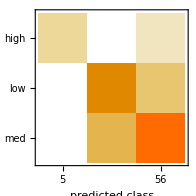

```mathematica
testSVM["ConfusionMatrixPlot"]
```

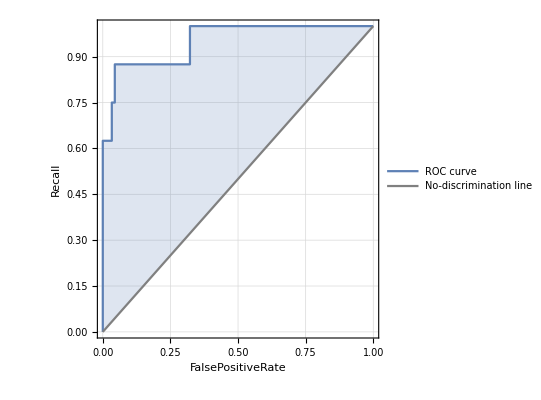
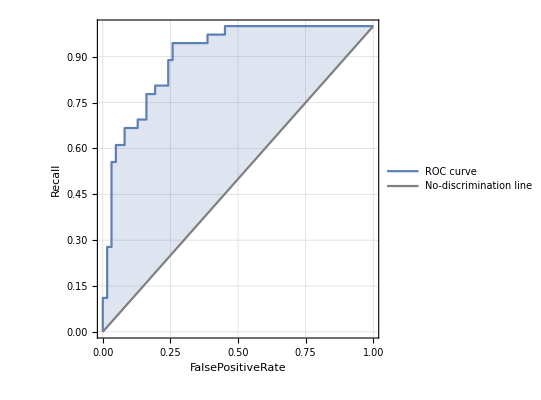
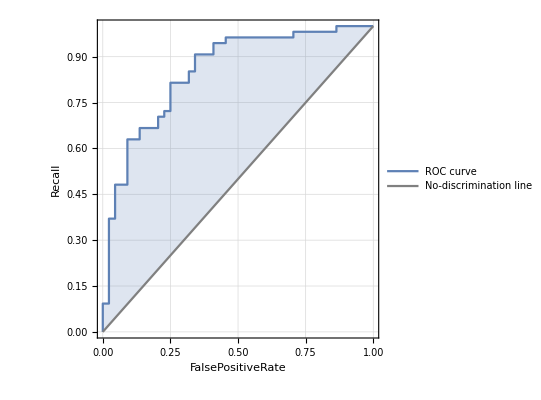
<|high→-Graphics-,low→-Graphics-,med→-Graphics-|>

```mathematica
testSVM["ROCCurve"]
```

By looking at the receiver operating curve for each class, we can say that medium class was the worst classification when compared to other classes. We get a good classification accuracy.

### Logistic Regression

Logistic model (or logit model) is a statistical model that models the probability of one event (out of two alternatives) taking place by having the log-odds (the logarithm of the odds) for the event be a linear combination of one or more independent variables (“predictors”). 

-Graphics-

#### Training

1 : Train the model with train dataset.

```mathematica
lr = Classify[trainFinal,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
Information[lr,"MethodDescription"]
```

The logistic regression classifier models class probabilities with logistic functions of linear combinations of features. It is also called log-linear model, softmax regression, or maximum-entropy classifier.

2 : About the classifier

```mathematica
Information[lr]
```

Classifier information
Data type | Mixed (number: 5)
Classes | ,,highlowmed
Accuracy | (74.4.) %
Method | LogisticRegression
Single evaluation time | 3.57 ms/example
Batch evaluation speed | 102. examples/ms
Loss | 0.492 ± 0.081
Model memory | 238. kB
Training examples used | 391 examples
Training time | 1.38 s
 |

#### Testing

We test the data by applying the classifier generated from the training set to the test set

```mathematica
testlr = ClassifierMeasurements[lr,testFinal];testlr[{"Accuracy","RejectionRate","AreaUnderROCCurve"}]
```

{0.755102,0.,<|high→0.947222,low→0.902778,med→0.872475|>}

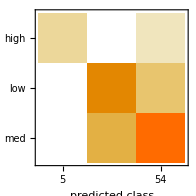

```mathematica
testlr["ConfusionMatrixPlot"]
```

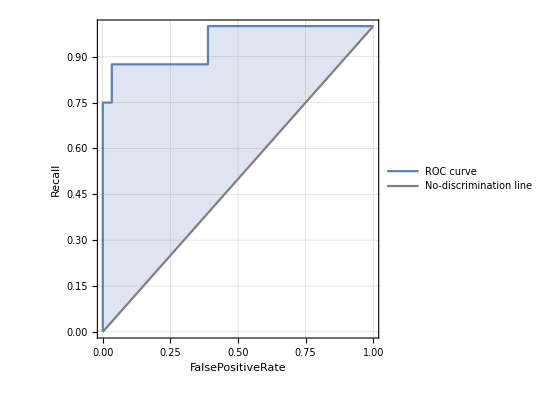
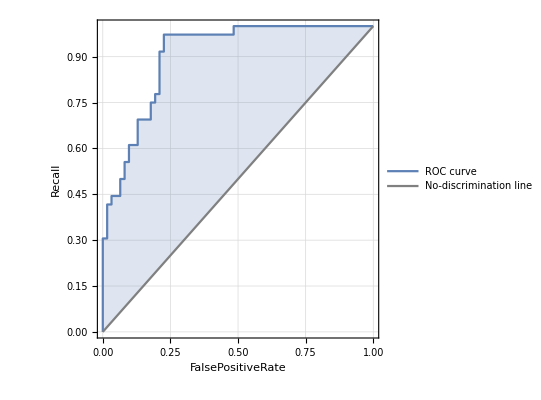
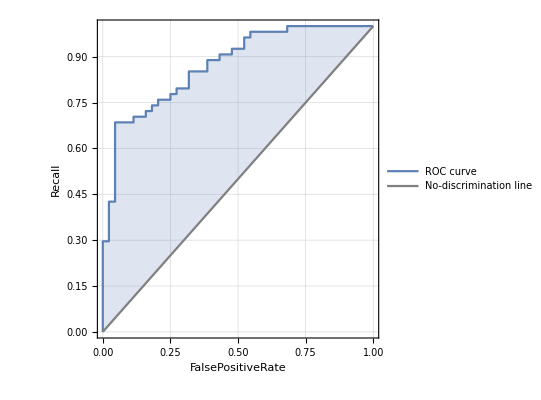
<|high→-Graphics-,low→-Graphics-,med→-Graphics-|>

```mathematica
testlr["ROCCurve"]
```

### Random Forest

Random forest is a Supervised Machine Learning Algorithm that is used widely in Classification and Regression problems. It builds decision trees on different samples and takes their majority vote for classification and average in case of regression.
-Graphics-

#### Training

1 : Train the model with train dataset.

```mathematica
rf = Classify[trainFinal,Method->"RandomForest"]
```

ClassifierFunction[…]

```mathematica
Information[rf,"MethodDescription"]
```

The random forest classifier uses an ensemble of decision trees to predict the class. Each decision tree has been trained on a random subset of the training set, and only uses a random subset of the features.

2 : About the classifier

```mathematica
Information[rf]
```

Classifier information
Data type | Mixed (number: 5)
Classes | ,,highlowmed
Accuracy | (80.63.3) %
Method | RandomForest
Single evaluation time | 5.62 ms/example
Batch evaluation speed | 20.3 examples/ms
Loss | 0.568 ± 0.035
Model memory | 254. kB
Training examples used | 391 examples
Training time | 544. ms
 |

#### Testing

We test the data by applying the classifier generated from the training set to the test set

```mathematica
testrf = ClassifierMeasurements[rf,testFinal];testrf[{"Accuracy","RejectionRate","AreaUnderROCCurve"}]
```

{0.836735,0.,<|high→0.984722,low→0.930556,med→0.887626|>}

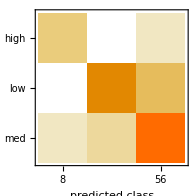

```mathematica
testrf["ConfusionMatrixPlot"]
```

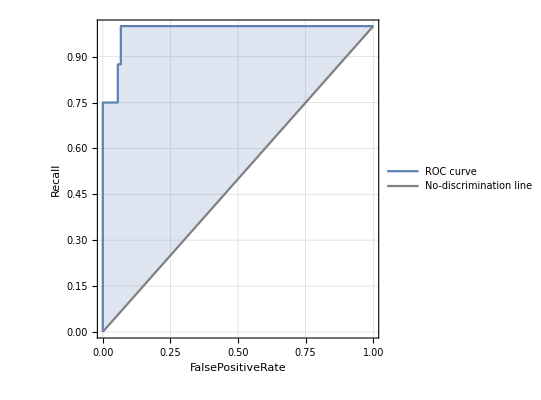
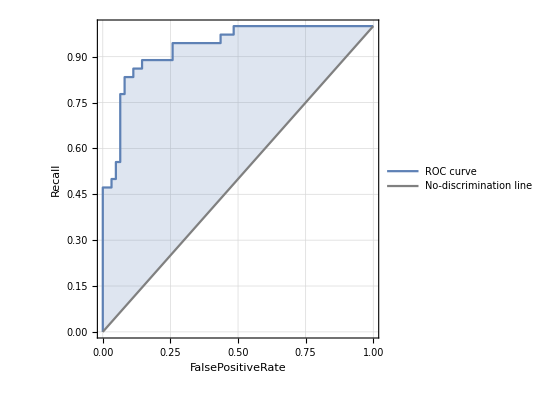
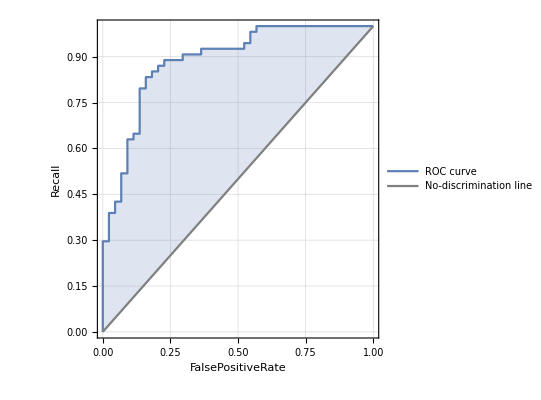
<|high→-Graphics-,low→-Graphics-,med→-Graphics-|>

```mathematica
testrf["ROCCurve"]
```

### Artificial Neural Network

Neural networks, also known as artificial neural networks (ANNs) or simulated neural networks (SNNs), are a subset of machine learning and are at the heart of deep learning algorithms. Their name and structure are inspired by the human brain, mimicking the way that biological neurons signal to one another.
-Graphics-

#### Training

1 : Train the model with train dataset.

```mathematica
ANN = Classify[trainFinal,Method->"NeuralNetwork"]
```

ClassifierFunction[…]

```mathematica
Information[ANN,"MethodDescription"]
```

An neural networks is composed of layers of artificial neuron units. Each 
unit computes its value as a function of the unit values in the previous layer. Information 
is processed layer by layer from the feature layer to the output layer which gives the class probabilities. It is 
also called a feed-forward neural network or a multi-layer perceptron.

2 : About the classifier

```mathematica
Information[ANN]
```

Classifier information
Data type | Mixed (number: 5)
Classes | ,,highlowmed
Accuracy | (85.6.) %
Method | NeuralNetwork
Single evaluation time | 4.6 ms/example
Batch evaluation speed | 28.4 examples/ms
Loss | 0.423 ± 0.12
Model memory | 472. kB
Training examples used | 391 examples
Training time | 27.6 s
 |

#### Testing

We test the data by applying the classifier generated from the training set to the test set

```mathematica
testANN = ClassifierMeasurements[lr,testFinal];testANN[{"Accuracy","RejectionRate","AreaUnderROCCurve"}]
```

{0.755102,0.,<|high→0.947222,low→0.902778,med→0.872475|>}

```mathematica
testANN["ConfusionMatrixPlot"]
```

-Graphics-

```mathematica
testANN["ROCCurve"]
```

<|high→-Graphics-,low→-Graphics-,med→-Graphics-|>

### Nearest Neighbour

The k-nearest neighbors algorithm is a non-parametric supervised learning method first developed by Evelyn Fix and Joseph Hodges in 1951, and later expanded by Thomas Cover. It is used for classification and regression. The principle behind nearest neighbor methods is to find a predefined number of training samples closest in distance to the new point, and predict the label from these.
-Graphics-

#### Training

1 : Train the model with train dataset.

```mathematica
NN = Classify[trainFinal,Method->"NearestNeighbors"]
```

ClassifierFunction[…]

```mathematica
Information[NN,"MethodDescription"]
```

The nearest neighbors predictor predicts the value of a new example by analyzing its nearest neighbors in the feature space. In its simplest form, it averages the values of the "k"-nearest neighbors.

2 : About the classifier

```mathematica
Information[NN]
```

Classifier information
Data type | Mixed (number: 5)
Classes | ,,highlowmed
Accuracy | (71.5.) %
Method | NearestNeighbors
Single evaluation time | 3.78 ms/example
Batch evaluation speed | 33.1 examples/ms
Loss | 0.543 ± 0.09
Model memory | 167. kB
Training examples used | 391 examples
Training time | 472. ms
 |

#### Testing

We test the data by applying the classifier generated from the training set to the test set

```mathematica
testNN = ClassifierMeasurements[NN,testFinal];testNN[{"Accuracy","RejectionRate","AreaUnderROCCurve"}]
```

{0.77551,0.,<|high→0.8875,low→0.903674,med→0.839226|>}

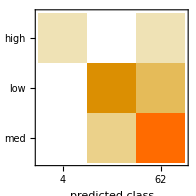

```mathematica
testNN["ConfusionMatrixPlot"]
```

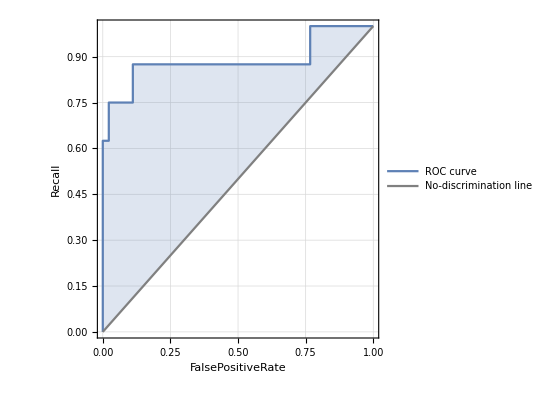
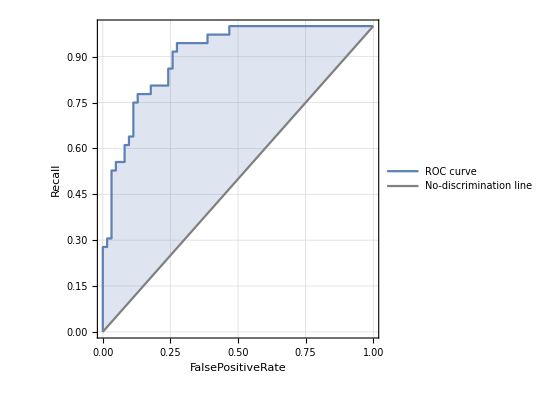
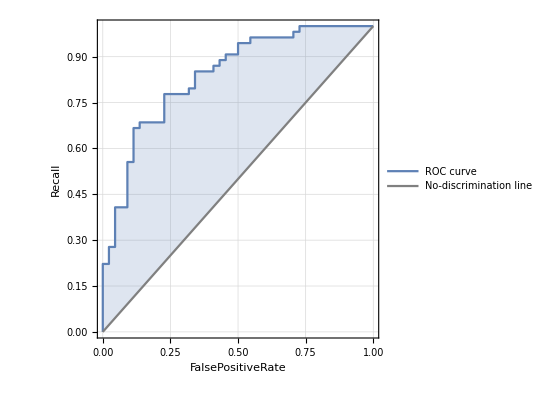
<|high→-Graphics-,low→-Graphics-,med→-Graphics-|>

```mathematica
testNN["ROCCurve"]
```

### Conclusion :

We can be sure to say from the above seem outputs, that dataset performs the best with any given MAchine Learning Algorithms. It is more advantages because of the less computational time each algorithm it consumes. Considering my dataset to be small, in real-time scenarios with big datasets and good computationally efficient computers, SVM would perform better than others without freezing the program.
The determination of the price classes helps in bettering the jobs of real estate managers / websites in suggesting houses based on individual needs. It saves time and increases efficiency. 
It’s a lot easier to visualize, manipulate, and explore neural nets with the magic under the hood of Mathematica. So for learning about deep learning and iterating on neural network designs, Mathematica may be a good companion to Python or R. For students getting to learn Machine Learning Algorithms, first hand with Mathematica understand better due to better and ease of visualization without complex code for visualizations when compared to other programming languages like R or Python.